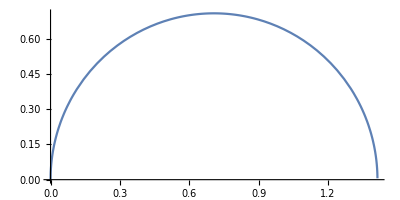

```mathematica
ParametricPlot[{x1, Sqrt[1/2 - (x1 - 1/Sqrt[2])^2]}, {x1, 0, Sqrt[2]}, AspectRatio->1/2]
```

```mathematica
{x1, (x1 - 1/Sqrt[2])^2/Sqrt[2]} /.x1->0
```

{0,1/(2 √2)}

```mathematica
{{1, 2}, {3, 4}}.{a, b}
```

{a+2 b,3 a+4 b}

```mathematica
(1/Sqrt[2]) {{1 , 1}, {-1, 1}}.{x1, Sqrt[1/2 - (x1 - 1/Sqrt[2])^2]}
```

{(x1+√(1/2-(-1/(√2)+x1)^2))/(√2),(-x1+√(1/2-(-1/(√2)+x1)^2))/(√2)}

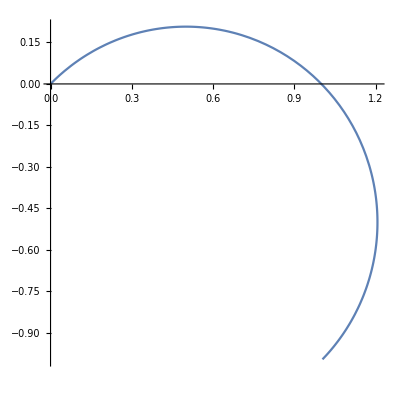

```mathematica
ParametricPlot[(1/Sqrt[2]) {{1 , 1}, {-1, 1}}.{x1, Sqrt[1/2 - (x1 - 1/Sqrt[2])^2]}, {x1, 0, Sqrt[2]}, AspectRatio->1]
```

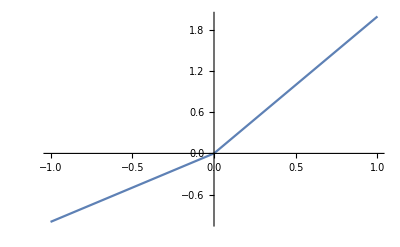

```mathematica
Plot[Piecewise[{{a, a<0}, {2a, a>=0}}], {a, -1, 1}]
```

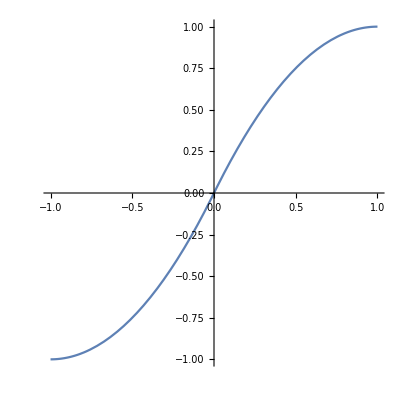

```mathematica
Plot[Piecewise[{{(1-s)a +s*a^2, a>=0}, {(1-s)a - s a^2, a<0}}]/.s->-1, {a, -1, 1}, AspectRatio->1]
```

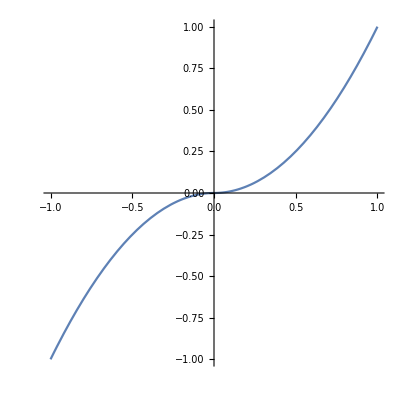

```mathematica
Plot[((1-s)a +Sign[a] * s*a^2)/.s->1, {a, -1, 1}, AspectRatio->1]
```